# Benford’s Law

Benford’s Law is an empirical law in statistics that states that the leading significant digit of numerical data in real life is likely to be small.

## Discovering Benford’s Law

In statistics, not a lot of attention is paid to the first digits of numbers. After all, they’re evenly distributed in the sequence of natural numbers.

Make a histogram of the first digits of the first 100000 natural numbers:

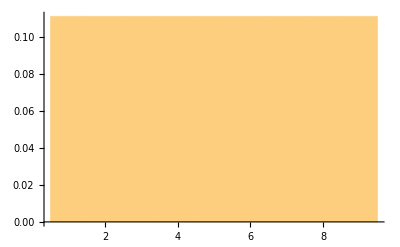

```mathematica
Histogram[Table[First[IntegerDigits[i]],{i,100000}],Automatic,"Probability"]
```

It’s a no-brainer that this statement still holds for random integers.

Make a histogram of the first digits of 100000 random integers up to 100000:

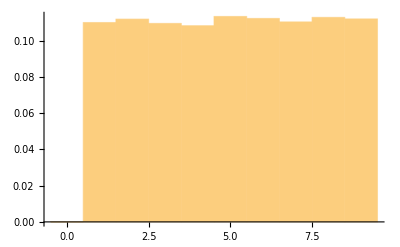

```mathematica
Histogram[Table[First[IntegerDigits[RandomInteger[100000]]],100000],Automatic,"Probability"]
```

The same applies to random real numbers.

Make a histogram of the first digits of 100000 random real numbers up to 100000:

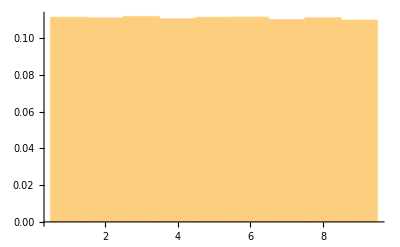

```mathematica
Histogram[Table[First[First[RealDigits[RandomReal[{0,100000}]]]],100000],Automatic,"Probability"]
```

This seems like a boring topic. But let’s take a look at some meaningful sequences, starting from the primes.

Make a histogram of the first digits of the first 100000 primes:

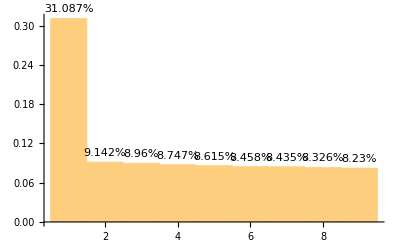

```mathematica
Histogram[Table[First[IntegerDigits[Prime[i]]],{i,100000}],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)]
```

There are significantly more primes that starts with 1 than primes that starts with other digits. What about the 
Fibonacci numbers?

Make a histogram of the first digits of the first 100000 Fibonacci numbers:

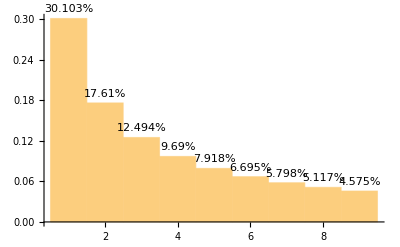

```mathematica
Histogram[Table[First[IntegerDigits[Fibonacci[i]]],{i,100000}],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)]
```

The decay is soother. What about factorials?

Make a histogram of the first digits of the first 10000 factorials:

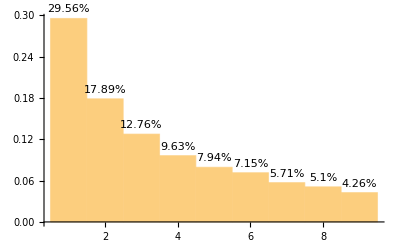

```mathematica
Histogram[Table[First[IntegerDigits[i!]],{i,10000}],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)]
```

The pattern is similar. What about powers of 2?

Make a histogram of the first digits of the first 10000 powers of 2:

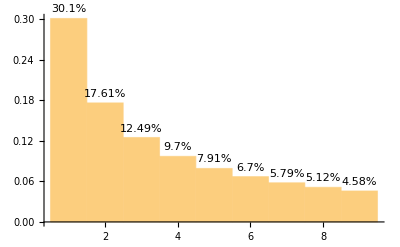

```mathematica
Histogram[Table[First[IntegerDigits[2^i]],{i,10000}],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)]
```

Now let’s move on to some data from real life, starting with the population of countries. tallest buildings random article

Make a histogram of the first digits of the populations of all the countries in the world:

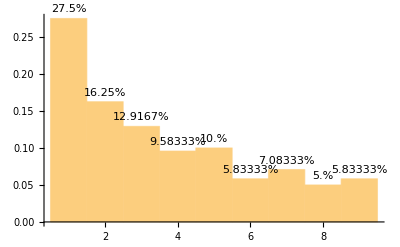

```mathematica
Histogram[First[IntegerDigits[First[#]]]&/@EntityClass["Country","Countries"][EntityProperty["Country","Population"]],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)]
```

The distribution is generally similar. What about the lengths of the longest rivers in the world?

Make a histogram of the first digits of the lengths of the top 1000 longest rivers in the world in both feet and meters:

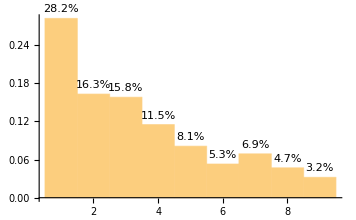
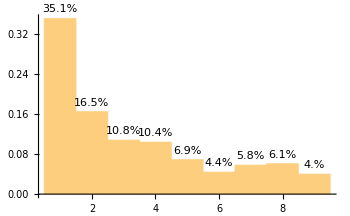

```mathematica
Table[Histogram[First[First[RealDigits[N[First[UnitConvert[#,u]]]]]]&/@["Length"],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)],{u,{"Feet","Meters"}}]
```

Even in a random Wikipedia page, some pattern can be seen.

Make a histogram of the first digits of the numbers in the Wikipedia page of “Random”:

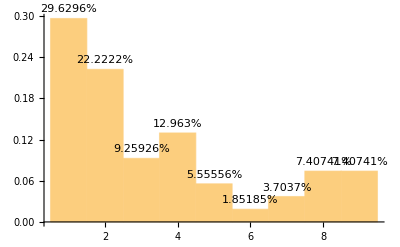

```mathematica
Histogram[First[IntegerDigits[ToExpression[#]]]&/@StringCases[WikipediaData["Random"],n:(DigitCharacter..)/;StringPart[n,1]≠"0"],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)]
```

Does this pattern apply to all sets of data? Finally let’s take a look at the heights of the tallest structures in the world.

Make a histogram of the first digits of the heights of the top 1000 tallest structures in the world in both feet and meters:

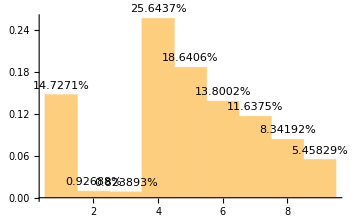
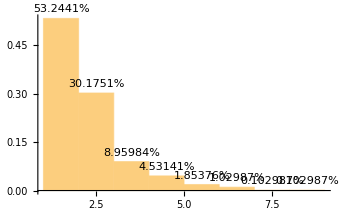

```mathematica
Table[Histogram[First[First[RealDigits[First[UnitConvert[#,u]]]]]&/@DeleteMissing[["Height"]],Automatic,"Probability",LabelingFunction->(Placed[Row[{100#,"%"}],Above]&)],{u,{"Feet","Meters"}}]
```

Not a very good fit, but the general trend holds.

## Benford’s Law

The probability density function of Benford Distribution:

```mathematica
PDF[BenfordDistribution[b],x]
```

Piecewise[{{Log[1+1/x]/Log[b], 1≤x<b}, {0, True}}]

Plot a Benford Distribution with base parameter 10:

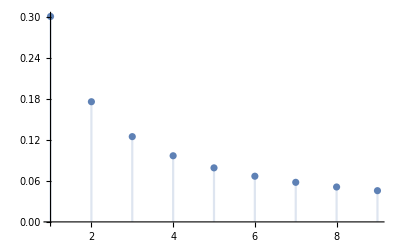

```mathematica
DiscretePlot[PDF[BenfordDistribution[10],x],{x,1,9}]
```

It is amazing how exactly the Fibonacci numbers, factorials, and powers of 2 fit Benford Distribution.

Combine the plot of Benford Distribution and the histograms above:

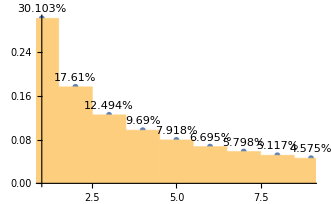
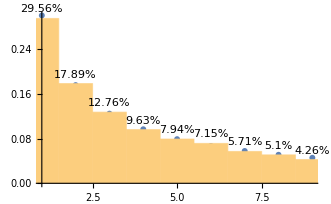
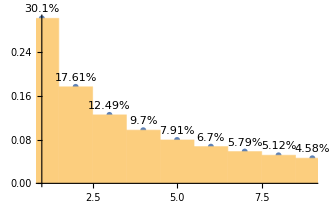

```mathematica
Show[%72,#]&/@{%97,%100,%101}
```

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Name of Author

Date of creation

Author email address (please use the email associated with your Wolfram User ID)